```mathematica
Clear[x,ω]
```

```mathematica
DSolve[x''[t]+ω^2 x[t]==0,x[t],t]
```

{{x[t]→C[1] Cos[t ω]+C[2] Sin[t ω]}}

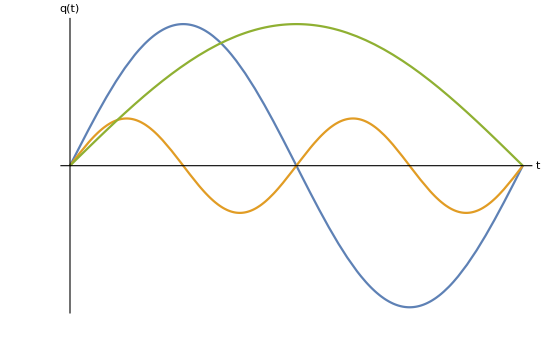
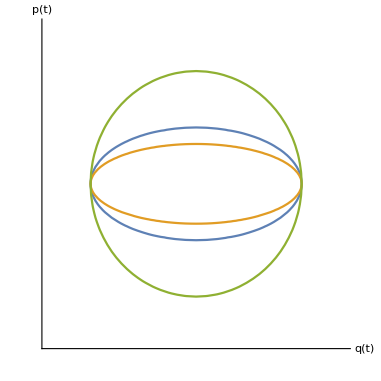

```mathematica
{Plot[{15 Sin[2 t],5Sin[4t],15Sin[t]},{t,0,π},Ticks->None,AxesLabel->{Style[t,FontSize->15],Style[q[t],FontSize->15]}],ContourPlot[{p^2/2+q^2/(2/4)==10,p^2/2+q^2/(2/8)==10,p^2/2+q^2/(2/1)==10},{p,-2π,2π},{q,-2π,2π},Axes->True,Frame->False,Ticks->None,AxesLabel->{Style[q[t],FontSize->15],Style[p[t],FontSize->15]}]}
```

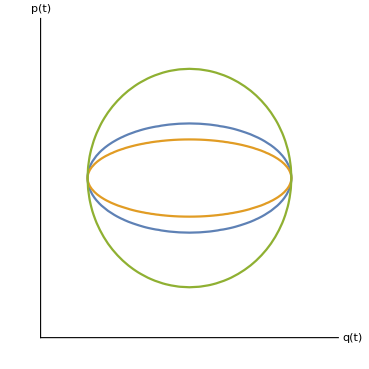

```mathematica
ContourPlot[{p^2/2+q^2/(2/4)==10,p^2/2+q^2/(2/8)==10,p^2/2+q^2/(2/1)==10},{p,-2π,2π},{q,-2π,2π},Axes->True,Frame->False,Ticks->None,AxesLabel->{Style[q[t],FontSize->15],Style[p[t],FontSize->15]}]
```

```mathematica
DSolve[x''[t]+γ x'[t]+ ω^2 x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(1/2 t (-γ-√(γ^2-4 ω^2))) C[1]+ⅇ^(1/2 t (-γ+√(γ^2-4 ω^2))) C[2]}}

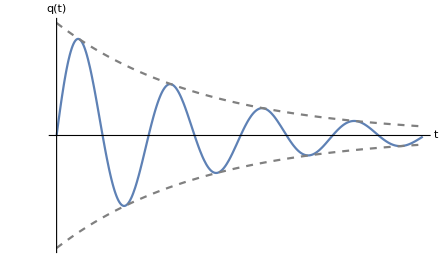
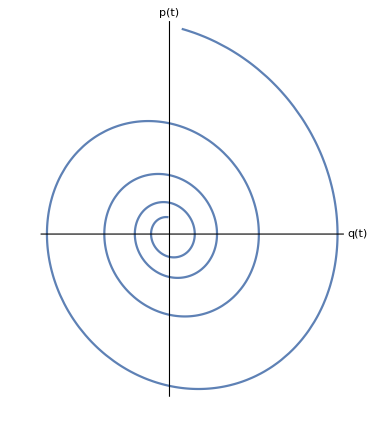

```mathematica
x[t_]:=ⅇ^(-ω ζ t)Sin[(ω √(1-ζ^2))t]
{Plot[{2x[t],2 ⅇ^(-ω ζ t),-2 ⅇ^(-ω ζ t)},{t,0,8π},PlotRange->All,PlotStyle->{0,{Dashed,Gray},{Dashed,Gray}},Ticks->None,AxesLabel->{Style[t,FontSize->15],Style[q[t],FontSize->15]}],ParametricPlot[{x[t],x'[t]},{t,-4π,4Pi},Ticks->None,AxesLabel->{Style[q[t],FontSize->15],Style[p[t],FontSize->15]}]}
```

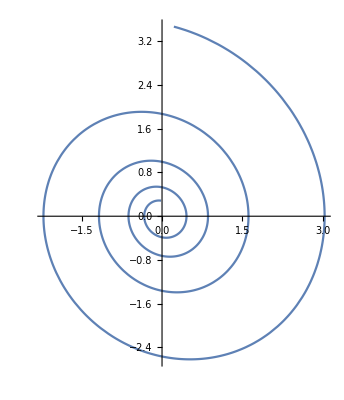

```mathematica
ParametricPlot[{x[t],x'[t]},{t,-4π,4Pi}]
ω=1;
ζ=0.1;
```